{25/2,{p→1/2}}

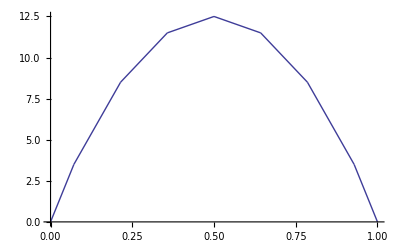

```mathematica
hH[k_,m_]:=Sum[Max[2*(m-k-t)-1, 0], {t,0,m}]
hL[k_,m_]:=Sum[Max[2*(k-t)-1, 0], {t,0,m}]
omega[k_,m_,p_]:=p*hH[k,m]+(1-p)*hL[k,m]
m=7;
omegaMin[p_]:=Min[omega[#,m,p]& /@ Range[0,m]]
Maximize[omegaMin[p],p]
Plot[omegaMin[p], {p,0,1},PlotPoints->500]
```